```mathematica
(*Checking thermal Gaussian calculation*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
kB=1.38064852 10^-23;(*[J/K] Boltzmann constant*)
AMU=1.66053906660 10^-27;
M=(83.9134191)AMU;
```

```mathematica
(*Checking normalization*)
FullSimplify[Integrate[1/((2π)^(3/2)Sqrt[σ0x^2+(kB T t^2)/m]Sqrt[σ0y^2+(kB T t^2)/m]Sqrt[σ0z^2+(kB T t^2)/m])Exp[-1/2(x^2/(σ0x^2+(kB T t^2)/m)+y^2/(σ0y^2+(kB T t^2)/m)+z^2/(σ0z^2+(kB T t^2)/m))],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}],{m>0,t≥0,kB>0,T>0,σ0x≥0,σ0y≥0,σ0z≥0}]
```

1

```mathematica
(*OD along x-axis by integrating out y and z axis.*)
FullSimplify[Integrate[1/((2π)^(3/2)Sqrt[σ0x^2+(kB T t^2)/m]Sqrt[σ0y^2+(kB T t^2)/m]Sqrt[σ0z^2+(kB T t^2)/m])Exp[-1/2(x^2/(σ0x^2+(kB T t^2)/m)+y^2/(σ0y^2+(kB T t^2)/m)+z^2/(σ0z^2+(kB T t^2)/m))],{y,-Infinity,Infinity},{z,-Infinity,Infinity}],{m>0,t≥0,kB>0,T>0,σ0x≥0,σ0y≥0,σ0z≥0}]
```

ConditionalExpression[(ⅇ^(-(m x^2)/(2 kB t^2 T+2 m σ0x^2)))/(√(2 π) √((kB t^2 T)/m+σ0x^2)),kB t^2 T+m σ0y^2>0]

```mathematica
FullSimplify[(ⅇ^(-(m x^2)/(2 kB t^2 T+2 m σ0x^2)))/(√(2 π) √((kB t^2 T)/m+σ0x^2))(1/(√(2 π) √((kB t^2 T)/m+σ0x^2))Exp[-1/2(x^2/(σ0x^2+(kB t^2 T)/m))])^-1]
```

1

```mathematica
(ⅇ^(-(m x^2)/(2 kB t^2 T+2 m σ0x^2)))/(√(2 π) √((kB t^2 T)/m+σ0x^2))/.{t->40 10^-3,x->0,kB->1.380649 10^-23,σ0x->0,m->(83.9134191)(1.66053906660 10^-27),T->150 10^-9}
```

2587.04

```mathematica
(ⅇ^(-(m x^2)/(2 kB t^2 T+2 m σ0x^2)))/(√(2 π) √((kB t^2 T)/m+σ0x^2))/.x->0
```

```mathematica
Solve[1/(√(2 π) √((kB t^2 T)/m+σ0x^2))A==1,A]
```

{{A→√(2 π) √((kB t^2 T+m σ0x^2)/m)}}

```mathematica
ⅇ^(-(m x^2)/(2 kB t^2 T+2 m σ0x^2))/.{t->40 10^-3,kB->1.380649 10^-23,σ0x->0,m->(83.9134191)(1.66053906660 10^-27),T->500 10^-9}
```

ⅇ^(-6.30779×10^6 x^2)

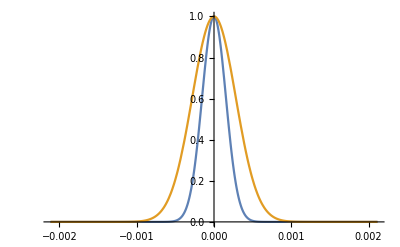

```mathematica
Plot[{ⅇ^(-2.1025967773659438*^7 x^2),ⅇ^(-6.30779033209783*^6 x^2)},{x,-2.1149999999999998 10^-3,2.1149999999999998 10^-3},PlotRange->Full]
```

```mathematica
(*Converting x sigmas to temperatures*)
σ[tdrop_,T_]:=Sqrt[0^2+(kB T)/M tdrop^2];
NSolve[σ[40 10^-3,T 10^-9]==36.9180(14.1 10^-6),T]
NSolve[σ[40 10^-3,T 10^-9]==31.0450(14.1 10^-6),T]
NSolve[σ[40 10^-3,T 10^-9]==27.2840(14.1 10^-6),T]
NSolve[σ[40 10^-3,T 10^-9]==24.5330(14.1 10^-6),T]
NSolve[σ[40 10^-3,T 10^-9]==18.3210(14.1 10^-6),T]
```

{{T→1709.2}}

{{T→1208.65}}

{{T→933.537}}

{{T→754.774}}

{{T→420.934}}

```mathematica
(*Converting x sigmas to temperatures*)
σ[tdrop_,T_]:=Sqrt[0^2+(kB T)/M tdrop^2];
NSolve[σ[40 10^-3,T 10^-9]==10.9620(14.1 10^-6),T]
NSolve[σ[40 10^-3,T 10^-9]==8.2416(14.1 10^-6),T]
NSolve[σ[40 10^-3,T 10^-9]==7.1601(14.1 10^-6),T]
NSolve[σ[40 10^-3,T 10^-9]==5.8428(14.1 10^-6),T]
NSolve[σ[40 10^-3,T 10^-9]==3.9994(14.1 10^-6),T]
```

{{T→150.694}}

{{T→85.1802}}

{{T→64.2915}}

{{T→42.8112}}

{{T→20.0588}}